(*notebook for creation of MCNPX input file with ICRP reference phantoms; purpose: calculation of organ doses from CT;
analog of bodyCalc.nb from 2008: calculates a batch of files *)

(*slices in AF are counted from feet*)

(*SYNOPSIS: Debug version;
check the validity of collimator surface description;
Can be used to generate CT input file or input file for calculator;
TO DO:fix AF “nslimax”: should not be 348 for AF;
test the calculation;
check the distance of phantom from the table to fit the trunk;
add write of "probabil.txt" file and MCNP execution;
test materials: could be errors in contents corresponding to element;
collimator, source and phantom lie in three different planes (2 layers 15M)
ERROR: if a fixed column is taken (nc=ncol or nc=1):ac should be written accordingly, then Left Adrenal with ac=1 is calculated;*)

### (*CHANGELOG*)

(*Previous version was saved on 25 April 2016;
changes on 15 November 2016: paths changed 
16 November 2016: indexes for reading complete phantom*)

(*2019 changes*)

```mathematica
(*7 Feb 2019: recent changes for thyroid;*)
(*29 Jul 2019: paths changed for /8core/debian 6.0*)
(*30 Jul 2019; fixed materials*)
(*5 Aug 2019: added shift over the table;*)
(*7 Aug 2019: added Carbon material;added R D U M cards;*)
(*12 Aug 2019: artificially changed the thickness of slice to 0.48*)
(*13 Aug 2019: introduced the CompressLine function*)
```

```mathematica
(*2020 changes*)
```

(*6 Feb 2020: finished writing short style lattice for MCNP; removed tally if no tissue is exposed;*)
(*22 Feb 2020: added setting of the volume for each organ*)
(*4 Mar 2020: fixed WriteMCNPCard to include three lines *)
(*9 Mar 2020: made a static long patient couch;*)
(*8 Apr 2020: minor correction to the procedure of writing the lattice;*)
(*4 Jun 2020: shifted phantom by 6 cm up to adjust it to the position of CT couch*)
(*18 Jun 2020: nslimax and nslimin are extremal;*)
(*26 Oct 2020: adding gender*)

```mathematica
(*3 May 2021; added more comments*)
(*8 June 2021: replaced png output with eps*)
(*13 Jul 2021: started Ages: added voxel count, sizes; *)
```

```mathematica
(*14 Jul 2021: MAJOR REVISION: removed directory to phantoms: from now they shoud be placed in the notebook directory;ammended synopsis*)
```

```mathematica
(*15 Jul 2021: added monitoring of processing lattice*)
```

```mathematica
(*16 Jul 2021: united with profile structure.nb*)
```

```mathematica
Needs["Units`"]
```

```mathematica
NotebookDirectory[]
```

/home/arkady/Documents/17 Jun/fantom110c-9ct/

```mathematica
(*TAMSIP*)
```

```mathematica
adresSpectrum="/home/arkady/Documents/calculator/TASMIP_Source"
```

/home/arkady/Documents/calculator/TASMIP_Source

```mathematica
voltage=80;
```

```mathematica
(*!!!CHANGE AppertZ TO 0.01 cm AND AppertX to 40 cm to get horizontal cross-section;*)
AppertZ={40};(*cm*)
AppertX={30};(*cm*)
(*!!!*)
RIP={150};(*cm*)
proection={"PA"};
```

```mathematica
Nproect=proection[[1]];
```

```mathematica
WriteMCNPCard[Line1_] := Module[{Line2, Line1M(*list for the words in Line*), i, NLines,Line3,NsymoblsinLine},NsymoblsinLine=73(*80-5-?*); Line3="";If[StringLength[Line1] >NsymoblsinLine, NLines = Quotient[StringLength[Line1], NsymoblsinLine]; Line1M = StringSplit[Line1, {" ","\n"}]; i =1;
Do[  Line2="";While[If[i>Length[Line1M],False,StringLength[Line2] <  NsymoblsinLine - StringLength[Line1M[[i]]] ],Line2 =StringTrim[ Line2 <> " " <> Line1M[[i]]];i = i +1;];Line3=StringTrim[Line3~~"     "~~Line2]~~"\n", {j, NLines +1}];Line3=StringTake[Line3,StringLength[Line3]-1];Return[Line3](*Find the last space before 80th position and split line into two at the position of the space*),Return[Line1]]];
```

```mathematica
(*turns 140 140 into 140 r*)
CompressLine[DummyArr_]:=Module[{DummyArrLen,DummyArrcurrent,times,Strout},DummyArrLen=Length[DummyArr];DummyArrcurrent=DummyArr[[1]];times=0;Strout="";Do[If[DummyArrcurrent==DummyArr[[i]],times++,
Strout=Strout~~" "~~ToString[DummyArrcurrent]~~" "~~Switch[times,0,"",1,"r ",_,ToString[times]~~"r "];DummyArrcurrent=DummyArr[[i]];times=0],{i,2,DummyArrLen}];Strout=Strout~~" "~~ToString[DummyArrcurrent]~~" "~~Switch[times,0,"",1,"r ",_,ToString[times]~~"r "]]
```

```mathematica
CT=False;(*Boolean: True or False*)
```

```mathematica
SplitFiles=True;(*Boolean: True or False;if true, .lat is written separately; if false, lattice is written into the main file*)
```

```mathematica
(*Hands=False;*)(*Boolean: True or False; not implemented?*)
```

```mathematica
Phantom="15M";(*AF;AM;00M;00F;01M;01F;05M;05F;10M;10F;15M;15F*)
```

```mathematica
(*ProceduresLst={"Lungs"};*)(*for work.txt*)
```

```mathematica
ProceduresLst={Phantom};
```

```mathematica
Switch[Phantom,"AM"||"00M"||"01M"||"05M"||"10M"||"15M",Gender=1,_,Gender=2];Print[Gender]
```

2

```mathematica
SetDirectory[NotebookDirectory[]<>Phantom]
```

/home/arkady/Documents/17 Jun/fantom110c-9ct/15M

```mathematica
ncol=Switch[Phantom,"AM",254,"AF",299,"00M"||"00F",345,"01M"||"01F",393,"05M"||"05F"||"10M"||"10F",419,"15M",407,_,401]
```

407

```mathematica
nrow=Switch[Phantom,"AM",127,"AF",137,"00M"||"00F",211,"01M"||"01F",248,"05M"||"05F",230,"10M"||"10F",226,"15M",225,_,236]
```

225

```mathematica
nsli=Switch[Phantom,"AM",222,"AF",348,"00M"||"00F",716,"01M"||"01F",546,"05M"||"05F",572,"10M"||"10F",576,"15M",586,_,571]
```

586

```mathematica
nn2= nrow   ncol
```

91575

```mathematica
(*voxelres cm*)
```

```mathematica
dvcol=Switch[Phantom,"AM",0.2137,"AF",0.1775,"00M"||"00F"||"01M"||"01F",0.0663,"05M"||"05F",0.085,"10M"||"10F",0.099,"15M",0.125,_,0.12]
```

0.125

```mathematica
dvrow=dvcol;(*should be removed only if not used for Mass change*)
```

```mathematica
(*Slice thickness, cm;AM 1st, AF - 2nd*)
```

```mathematica
dvsl=Switch[Phantom,"AM",0.8,"AF",0.484,"00M"||"00F",0.0663,"01M"||"01F",0.14,"05M"||"05F",0.1928,"10M"||"10F",0.2425,"15M",0.2832,_,0.2828]
```

0.2832

```mathematica
Kcent=273
```

273

```mathematica
Zcent=(nsli-Kcent) dvsl(*cm from top; used for determination of sdef position;*)
```

88.6416

```mathematica
Zcentr=Zcent(*was an index for CT: to calculate the row of coefficients from 1 to 160 cm*)
```

88.6416

## (* reading of initial phantom *)

```mathematica
(* Creation of Surfaces and Source and Tally *)
```

```mathematica
(*scatteredfield=15.55;*)(*cm; guess from Makarevich;which projection?*)
```

```mathematica
ImageGap=1;(*somewhere in report it was 5 cm, but in CreatePhantomMale.nb it is 1 from skin plane, not from box*)
```

```mathematica
(*setting the position of the source depending on the projection*)
srcx=0;(*only two projections -AP and PA, we make x position constant*)
```

```mathematica
If[Nproect=="AP",srcy=-(RIP[[1]]-3-ImageGap);vec=" vec=0 1 0 ",srcy=RIP[[1]]-3-ImageGap;vec=" vec= 0 -1 0 "]
```

vec= 0 -1 0

```mathematica
eps=.0002;(*small parameter for lattice to include less than the volume of the voxels*)
```

```mathematica
dvcolB=dvcol-eps;(*a value less than the size of voxel along x axis*)
```

```mathematica
dvrowB=dvrow-eps;(*a value less than the size of voxel along y axis*)
```

```mathematica
dvslB=dvsl-  eps;(*a value less than the size of voxel along z axis*)
```

```mathematica
(*5.781658 is arbitrary value was selected in ~2017 to center phantom head in CT axis*)
```

```mathematica
(*3 cm for the line of phantom to lie below the table;*)
```

```mathematica
(*6.36325 is the solution of system of equations {(x-0)^2+(y-43)^2==51.1^2,x==-13.2087}*)
```

```mathematica
dy=5.78165+(6.36325)-3(*for head 5.78165;*)(*for CT shift?*)
```

9.1449

```mathematica
dx=0;
```

```mathematica
nsli*dvsl
```

165.955

```mathematica
dz=163.544;(*for CT shift?*)
```

```mathematica
If[Length[StringPosition[Phantom,"A"]]>=1,fantom1=ReadList[Phantom~~".dat",Number,RecordSeparators->{"\n","   "}];,fantom1=ReadList[Phantom~~"_ascii.dat",Number,RecordSeparators->{"\n"," "}];]
```

```mathematica
nsliMin=1;(*Round[Kcent-(AppertZ[[1]]/2+scatteredfield)/dvsl]:;nsli-19:2018 female calculation*)
```

```mathematica
Kcent-(AppertZ⟦1⟧/2+scatteredfield)/dvsl
```

273-3.53107 (20+scatteredfield)

```mathematica
(*nsliMin=nsli-172*)(*to include all Skin,trunk;292*)
```

```mathematica
(*Min[Round[Kcent+(AppertZ[[1]]/2+scatteredfield)/dvsl],nsli]*)
```

```mathematica
(*nsli/2 is OK for 15M*)
```

```mathematica
nsliMax=10;
```

```mathematica
min(Round[(AppertZ⟦1⟧/2+scatteredfield)/dvsl+Kcent],nsli)
```

Min[586,Round[273+3.53107 (20+scatteredfield)]]

```mathematica
(* 3D array of voxels  for given sections;  *)
```

```mathematica
(* x-anterior posterior-back row, y-left-right-column, z -down-up -slides -*)
```

```mathematica
(*coordinate system is right:x(columns) goes from spine to hand;y(rows) goes from spine to nose;z goes from legs to top*)
```

```mathematica
ncolMin=1;(*should be 1*)
ncolMax=ncol;(*should be ncol*)
```

```mathematica
ac=ConstantArray[1,{ ncolMax-ncolMin+1, nrow ,nsliMax-nsliMin+1}];(*deside to change ncol to ncolMax-ncolmin+1*)
```

```mathematica
(*Do[Switch[
fantom1[[i] ],0,
fantom2[[i-nrow (nsliMin-1) (ncolMax-ncolMin+1)]]=140,141,fantom2[[i-nrow (nsliMin-1) (ncolMax-ncolMin+1)]]=122,_,
 fantom2[[i-nrow (nsliMin-1) (ncolMax-ncolMin+1)]]=fantom1[[i]]
]
,{i,nrow (nsliMin-1) (ncolMax-ncolMin+1)+1,nrow nsliMax (ncolMax-ncolMin+1)}]  ; *)(*fantom2 should be kept*)
```

```mathematica
Timing[Do[ 
        Do[    
                           Do[    iw=nn2  (isl-1) + ncol* (ir-1)  +ic;
                                 Switch[
fantom1[[iw] ],0,
 ac[[ic]][[ir]][[isl-nsliMin+1]]=140,141,ac[[ic]][[ir]][[isl-nsliMin+1]]=122,_,
  ac[[ic]][[ir]][[isl-nsliMin+1]]=fantom1[[iw]]
]
                            , {ic,ncolMin-ncolMin+1,ncolMax-ncolMin+1}]
         ,{ir,1,nrow}];Print["end processing slice " ,isl];
,{isl,nsliMin,nsliMax}]  ; 
orgSections=Union[Flatten[ac]];]
```

end processing slice 1

end processing slice 2

end processing slice 3

end processing slice 4

end processing slice 5

end processing slice 6

end processing slice 7

end processing slice 8

end processing slice 9

end processing slice 10

{6.752,Null}

```mathematica
plot=ArrayPlot[ac[[Round[ncol/2],All,All]],AspectRatio->dvcol nrow/dvsl/nsli,DataReversed->{False,True},ImageSize->1024]
```

-Graphics-

```mathematica
Directory[]
```

/home/arkady/Documents/17 Jun/fantom110c-9ct/15M

```mathematica
(*Export["Phantom_"<>Phantom<>"_sagittal.eps",plot]*)
```

```mathematica
(* Selection organs of given sections *)
cell0= Import[Phantom<>"_organs.dat","Table"];
cell={};
Do[   
 Do[ If[ orgSections[[ik]]==cell0[[io]][[1]],AppendTo[ cell,cell0[[io]]],Null],{ik,1,Length[orgSections]}]
,{io,5,Length[cell0]}]
```

```mathematica
(*Timing[volcell=Table[Count[Take[fantom1,{nrow (nsliMin-1) (ncolMax-ncolMin+1)+1,nrow nsliMax (ncolMax-ncolMin+1)}],cell[[i,1]]],{i,Length[cell]}]]*)
```

```mathematica
volcell={1168,1025,443,2714,1128,742,1580,1567,4155,1853,20424,29356,18954,29940,4026,21456,12626,3474,27442,16438,3342,15991,12154,5215,3695,66358,76182,39269,42959,9978,30440,52376,7774,59138,62412,15112,26994,76686,6507,5248,24334,90804,20918,34162,14570,18190,4108,9528,10801,45257,4409,44549,8654,21908,2821,7433,6962,28078,308380,1091,604,1177,612,49,1435,49,1435,1690,9840,26237,43582,113290,148435,16738,9931,9968,5920,16815,12949,9818,6203,10790,18135,1392,49969,91401,19977,7145,1420,19935,7155,1427,279448,3921,251814,2675,332488,2531,2490,923,21606,1858,1860,194733,1427176,811048,2732527,6521,24094,110,942,32723,2977794,208949,502221,7481,7545,23765,128164,78486,150418,10484,27625,3393,1738,1736,7710,2584,11934,664,504,515,8645,34304,86773}
```

{1168,1025,443,2714,1128,742,1580,1567,4155,1853,20424,29356,18954,29940,4026,21456,12626,3474,27442,16438,3342,15991,12154,5215,3695,66358,76182,39269,42959,9978,30440,52376,7774,59138,62412,15112,26994,76686,6507,5248,24334,90804,20918,34162,14570,18190,4108,9528,10801,45257,4409,44549,8654,21908,2821,7433,6962,28078,308380,1091,604,1177,612,49,1435,49,1435,1690,9840,26237,43582,113290,148435,16738,9931,9968,5920,16815,12949,9818,6203,10790,18135,1392,49969,91401,19977,7145,1420,19935,7155,1427,279448,3921,251814,2675,332488,2531,2490,923,21606,1858,1860,194733,1427176,811048,2732527,6521,24094,110,942,32723,2977794,208949,502221,7481,7545,23765,128164,78486,150418,10484,27625,3393,1738,1736,7710,2584,11934,664,504,515,8645,34304,86773}

```mathematica
(* READING OF SPECTRUM *)
```

```mathematica
(*recovered from "fantom110c-8ct.nb" 7 Feb 2019*)
```

```mathematica
Directory[]
```

/home/arkady/Documents/17 Jun/fantom110c-9ct/15M

```mathematica
spAdress={"x100_Al2p5_W.txt","x105_Al2p5_W.txt","x109_Al1p4_W.txt","x109_Al2p5_W.txt",
"x109_W.txt","x110_Al2p5_W.txt","x115_Al2p5_W.txt","x120_Al2p5_W.txt",
"x125_Al2p5_W.txt","x130_Al2p5_W.txt","x135_Al2p5_W.txt","x140_Al2p5_W.txt",
"x30_Al2p5_W.txt","x35_Al2p5_W.txt","x40_Al2p5_W.txt","x40_Re_m.txt",
"x40_W_m.txt","x40_W.txt","x45_Al2p5_W.txt","x50_Al2p5_W.txt","x55_Al2p5_W.txt",
"x60_Al1p4_W.txt","x60_Al2p5_W.txt","x60_W.txt","x63_Al1p4_W.txt","x63_Al2p5_W.txt",
"x63_W.txt","x65_Al2p5_W.txt","x70_Al1p4_W.txt","x70_Al2p5_W.txt","x70_Al3_W.txt","x75_Al2p5_W.txt",
"x77_Al1p4_W.txt","x77_Al2p5_W.txt","x77_W.txt","x80_Al2p5_W.txt","x80_Al3_W.txt","x81_Al1p4_W.txt",
"x81_Al2p5_W.txt","x85_Al1p4_W.txt","x85_Al2p5_W.txt","x85_W.txt","x90_Al1p4_W.txt",
"x90_Al2p5_W.txt","x90_W.txt","x95_Al2p5_W.txt","x96_Al1p4_W.txt","x96_Al2p5_W.txt","x110_Al0p5_W.txt","x110_Al1p4_W.txt","x110_Al2p5_W.txt","x110_Al3_W.txt","x110_Al4_W.txt","x110_Al5_W.txt","x110_Al6_W.txt","x110_W.txt","x120_Al0p5_W.txt","x120_Al1p4_W.txt","x120_Al2p5_W.txt","x120_Al3_W.txt","x120_Al4_W.txt","x120_Al5_W.txt","x120_Al6_W.txt","x120_W.txt"};
```

```mathematica
vv0=voltage;    (* ParametersRegInsp[[iq]][[7]];*)
vv1=voltage;   (* ParametersRegInsp[[iq]][[8]]; *)
Print["V0==",vv0,"  V1==",vv1];
```

V0==80  V1==80

```mathematica
ener=IntegerPart[vv0];
adresSp="x"~~ToString[ener]~~"_";
Clear[fu];fu[x_]:=StringTake[x,{2,4}];
If[ener<100,EEE=ToString[ener]~~"_",EEE=ToString[ener]];
enerArray=Map[fu,spAdress];
cc=Flatten[Position[enerArray,EEE]];
adresFile=Part[spAdress,cc];
dAluminium="3";(*!!! fixed filter*)
If[dAluminium≠ 0,If[dAluminium=="2p5",at=StringReplacePart[dAluminium,"p",{2,2}],at=dAluminium];adresSp=adresSp~~"Al"~~at~~"_W",
adresSp=adresSp~~"W"];
adresSp=adresSp~~".txt";val= SetDirectory[adresSpectrum] ;
If[Position[spAdress,adresSp]=={}||val==Symbol["$Failed"],Print["SpectrumFile is absent"],Print["SPECTRUM Ok"];];


Print[%];
iop=OpenRead[adresSp];

aw1= Read[iop,Record];
bw1= Read[iop,Record];
spectrum={};
aw= Read[iop,Real];bw= Read[iop,Number];
While[aw≠ "EOF",AppendTo[spectrum,{aw*10^-6,bw}];aw= Read[iop,Real];bw= Read[iop,Number]];Close[iop];
Print[%];
```

If[/home/arkady/Documents/calculator/TASMIP_Source==$Failed,Print[SpectrumFile is absent],Print[SPECTRUM Ok];]

x80_Al3_W.txt

```mathematica
SetDirectory[NotebookDirectory[]<>Phantom];
```

```mathematica
(* Creation of Input File *)
```

```mathematica
(* Creation of Cells *)
```

```mathematica
(* Media to be used *)
numMed={};
Do[ AppendTo[numMed,cell[[ii]][[-2]]];
  ,{ii,1,Length[cell]}]
```

```mathematica
numMed=Union[numMed]
```

{2,12,27,29,57}

```mathematica
box="num box of fantom";
```

```mathematica
(*nr1=-68 for AF*)
```

```mathematica
nr1=-Round[nrow/2]
```

-112

```mathematica
nr2=Round[nrow/2]
```

112

```mathematica
ns1=-nsliMax+nsliMin
```

-9

```mathematica
ns2=0;
```

```mathematica
nc1=Round[N[ncol/2]]-ncolMax;(*??? check male *)
```

```mathematica
nc2=Round[N[ncol/2]]-ncolMin;
```

```mathematica
(* Start of writing into inp-file *)
```

```mathematica
ipp=OpenWrite[ProceduresLst[[1]]~~"_"~~ToString[Zcentr]];
```

```mathematica
WriteString[ipp,"phantom_for_*F8_calculations  "~~ToString[Length[volcell]]~~"\nc "~~Phantom~~" \nc mode="];
```

```mathematica
If[CT,WriteString[ipp,"CT","calculator"]]
```

```mathematica
(*If[CT,WriteString[ipp," Zcentr="<>ToString[Zcentr]],WriteString[ipp," Zcentr="<>ToString[Zcent]]];*)
```

```mathematica
WriteString[ipp,"; Date:"~~ToString[DateValue["Day"]]~~" "~~ToString[DateValue["MonthName"]]~~" "~~ToString[DateValue["Year"]]~~"; Kcent="~~ToString[Kcent]~~";\nc cells\n"];
```

```mathematica
(*table or collimator*)
```

```mathematica
If[CT,WriteString[ipp,"209 54     -1.4         8 -9 210 -211 -12 imp:p=1 vol=1 $ inner table shell\n    210 54      -1.4 13 -14 210 -211 -12 imp:p=1 vol=1 $ outer table shell\n"],WriteString[ipp, "160 80 -11.3 -160 170 imp:p=1 vol=1\n170 "<>numAir<>" -.001 -170 imp:p=1 vol=1\n"]];
```

```mathematica
Do[   ww=cell[[ic]];work="    "~~ToString[cell[[ic]][[1]]]~~"  ";word="  $ ";ss=-1;
              Do[ If[ NumberQ[ ww[[ik]]] ,If[cell[[ic,1]]==140,work="140 0 ",ss=ss*(-1);work=work~~ToString[ss*ww[[ik]]]~~"   "],word=word~~ToString[ww[[ik]]]~~" "] ,{ik,2,Length[ww]}];
work=work~~"-32  u="~~ToString[cell[[ic]][[1]]]~~"     imp:p=1 vol="~~ToString[dvrow dvcol dvsl volcell[[ic]]]~~word~~"\n";
WriteString[ipp,work]
,{ic,1,Length[cell]}];
```

```mathematica
If[Position[Phantom,"A"]≠{},numAir="53",numAir="57"]
```

57

```mathematica
If[CT,WriteString[ipp,"200 "<>numAir<>" -.001  40 -41 50 -51 60 -61 (-8:9:-210:211:12) (-13:14:-210:211:12) "];WriteString[ipp,"&\nimp:p=1 vol=1 fill=200 $ BOX\n198 "<>numAir<>" -.001 -70 #200 (-8:9:-210:211:12) (-13:14:-210:211:12)  imp:p=1&\n vol=1$ inside vac Sphere\n"];, WriteString[ipp,"200 "<>numAir<>" -.001  40 -41 50 -51 60 -61 170 160&\nimp:p=1 vol=1 fill=200 $ BOX\n198 "<>numAir<>" -.001 -70 #200 170 160 imp:p=1&\n vol=1$ inside vac Sphere\n"]]
```

```mathematica
WriteString[ipp,"199  0  70 imp:p=0 vol=0"~~"\n"];
```

```mathematica
(* Creation of Lattice *)
```

```mathematica
Directory[]
```

/home/arkady/Documents/17 Jun/fantom110c-9ct/15M

```mathematica
If[SplitFiles,latfilename=ToLowerCase[Phantom]~~".lat";WriteString[ipp,"read file="~~latfilename~~" noecho\n"];If[Length[Position[FileNames[],latfilename]]==0,LatticeFileStream=OpenWrite[latfilename],LatticeFileStream="stderr";];,LatticeFileStream=ipp;]
```

```mathematica
WriteString[LatticeFileStream,"150 "<>numAir~~" -.001 110 -111 120 -121 -131 130 u=200 imp:p=1 vol=1\n"~~"      "~~"lat=1  "~~
"fill="~~ToString[nc1]~~":"~~ToString[nc2]~~"  "~~ToString[nr1]~~":"~~ToString[nr2]~~"  "~~ToString[ns1]~~
":"~~ToString[ns2]~~"  $ the lattice "~~"\n"];
```

```mathematica
(*Do[www1="";Do[www="";Do[ www=www~~ToString[ac[[ic]][[ir]][[isl]]]~~" ",{ic,ncolMax,ncolMin,-1}];www=CompressLine[StringSplit[www," "]];www=StringReplace[www,"  "->" "];www1=www1~~"     "~~WriteMCNPCard[www];www="\nc end row "~~ToString[ir]~~"\n";www1=www1~~www,{ir,nrow,1,-1}];www="c end slice "~~ToString[isl]~~"\n";www1=www1~~www;WriteString[LatticeFileStream,www1];
,{isl,1,nsliMax-nsliMin+1}] ;*)
```

```mathematica
Timing[Do[www1 = " "; Do[               www = "       ";          
                             Do[ www = www ~~ " " ~~ ToString[ac[[ic,ir,isl]]];
                            If[StringLength[www] >= 75, www = www ~~ "\n"; www1 = www1 ~~ www; www = "       "]   
                                  , {ic, ncolMin, ncolMax}];
                                  If[StringLength[www]  >  8, www = www ~~ "\n"; www1 = www1 ~~ www];
   www = "c end row" ~~ ToString[ir] ~~ "\n";
   www1 = www1 ~~ www
            , {ir, 1, nrow}];
  www = "c end slice" ~~ ToString[isl] ~~ "\n";
  www1 = www1 ~~ www;
  
  WriteString[LatticeFileStream, www1]
  , {isl, 1, nsliMax - nsliMin + 1}] ;]
```

{11.248,Null}

```mathematica
(*creation of an array *)
```

```mathematica
(*Timing[densityInd=Table[Table[Table[Last[
cell[[
Position[cell[[All,1]],ac[[ic,ir,isl]]][[1,1]]
]]
], {ic, ncolMin, ncolMax}], {ir, 1, nrow}],{isl, 1, nsliMax - nsliMin + 1}] ;]*)
```

```mathematica
{1208.716,Null}(*15M 4 core*)
```

{1208.72,Null}

```mathematica
(*Possibly move this block after the phantom write*)
```

```mathematica
(*for electron source;AF*)(*Cases[ac[[ic,ir,isl]],{val_/;(val<13||val>52)&&(val<54||val>56)}]*)
```

```mathematica
(*Timing[ipp4=OpenWrite["body_sdef_cell_sp_par_3.dat"];WriteLine[ipp4,"sp4 &"];Do[Do[Do[If[ac[[ic,ir,isl]]≠140,If[(ac[[ic,ir,isl]]<13||ac[[ic,ir,isl]]>56),sp=ToString[densityInd[[isl,ir,ic]]],sp="0"];Timing[WriteLine[ipp4,sp<>" &"]]];, {ic, ncolMin, ncolMax}], {ir, 1, nrow}],{isl, 1,nsliMax - nsliMin +  1}] ;Close[ipp4]]*)
```

```mathematica
If[SplitFiles,Close[LatticeFileStream]]
```

15m.lat

```mathematica
(*!!! check the validity of resulting phantom*)
```

```mathematica
(* Creation of Surfaces and Source and Tally *)
```

```mathematica
(* dimensions of Base VOXEL *)
```

```mathematica
axVB=ToString[dvcol/2.](*AF phantom has odd number of voxels in that direction, so the voxel lies in the middle of X axis*)
```

0.0625

```mathematica
ayVB=ToString[dvrow/2.+dy]
```

9.2074

```mathematica
azVdownB=ToString[SetPrecision[(dvsl(nsliMax))-dz,7]]
```

-160.7120

```mathematica
azVupB=ToString[SetPrecision[(dvsl (nsliMax)+dvsl)-dz,7]]
```

-160.4288

```mathematica
ToExpression[azVupB]-ToExpression[azVdownB]
```

0.2832

```mathematica
(* dimensions of BOX *)
```

```mathematica
axB=ToString[dvcol (nc1+1)-dvcolB/1000.]
```

-25.2501

```mathematica
(*Max[,nc1 dvcol/2.-eps] along x axis*)
```

```mathematica
axB1=ToString[dvcol (nc2-1)-dvcolB/1000.]
```

25.2499

```mathematica
(*Max[,nc2 dvcol/2.-eps]*)(*axB is from the positive size of the col count*)
```

```mathematica
ayB=ToString[(dvrowB nrow)/2. -dvrowB/1000.-dy+0.00003]
```

4.89501

```mathematica
azB1=ToString[(dvsl (nsliMin))+eps-dz]
```

-163.261

```mathematica
(*position of z plane which corresponds to the position of base voxel*)
```

```mathematica
azB2=ToString[Round[(dvsl (nsliMax+1))-dvslB/1000.-dz,0.01]]
```

-160.43

```mathematica
(*azB2=ToString[Round[(dvsl (nsliMax)+dvslB/2.)-dvslB/100.-0.0001-dz,0.01]]*)
(* dimensions of VACCUUM SPHERA *)
radVacSph=Max[Sqrt[((dvcol ncol)/2.)^2 + ((dvrow nrow)/2.)^2+ ((dvsl nsli)/2.)^2],250](*for pediatric phantoms collimator appears outside the sphere*)
```

250

```mathematica
WriteString[ipp,"\n"~~"c  surfaces"~~"\n"]
```

```mathematica
(*creation of Table*)
```

```mathematica
If[CT,WriteString[ipp,"1 rcc 0 0 -30 0 0 50 75 $ universe\n8 c/z 0 43 51.1\n9 c/z 0 43 51.4\n210 pz "~~ToString[Round[(dvsl)-dvslB/2. +dvslB/1000.+0.0001-dz,0.01]]~~"\n211 pz "~~azB2~~"\n12 py -3\n13  c/z 0 23.3 35\n14  c/z 0 23.3 35.3\n"]]
```

```mathematica
(* creation of voxel *)
```

```mathematica
y0=((dy-dvrowB/2.)+Evaluate[ToExpression[ayVB]])/2;(*position of center of base voxel*)
```

```mathematica
z0=(Evaluate[ToExpression[azVupB]]+Evaluate[ToExpression[azVdownB]])/2
```

-160.57

```mathematica
R=√((Evaluate[ToExpression[axVB]])^2+(Evaluate[ToExpression[azVupB]]-Evaluate[ToExpression[azVdownB]])^2/4+((dy-dvrowB/2.)-Evaluate[ToExpression[ayVB]])^2/4)+eps;
```

```mathematica
WriteString[ipp,"c  voxel \n"];
```

```mathematica
WriteString[ipp,"32 s 0 "~~ToString[y0]~~" "~~ToString[z0]~~" "~~ToString[R]~~"\n"];
```

```mathematica
(* creation of Base voxel *)
```

```mathematica
WriteString[ipp,"c  Base voxel \n"]
```

```mathematica
WriteString[ipp,"110 px -"~~axVB~~" $ voxel surf 1; column\n"]
```

```mathematica
WriteString[ipp,"111 px  " ~~axVB~~ " $ voxel surf 2; column\n"]
```

```mathematica
WriteString[ipp,"120 py "~~ToString[dy-dvrow/2.]~~" $ voxel surf 3; row\n"]
```

```mathematica
WriteString[ipp,"121 py " ~~ayVB~~ " $ voxel surf 4; column\n"]
```

```mathematica
WriteString[ipp,"130 pz "~~azVdownB~~" $ voxel surf 5 " ~~"\n"~~"131 pz " ~~azVupB~~ " $ voxel surf 6 " ~~"\n"]
```

```mathematica
(* creation of BOX *)
```

```mathematica
WriteString[ipp,"c  Box\n"];
```

```mathematica
WriteString[ipp,"40 px "~~axB~~ "  $ Box surf 1 " ~~"\n"]
```

```mathematica
WriteString[ipp,"41 px  " ~~axB1~~ "  $ Box surf 2 " ~~"\n"]
```

```mathematica
WriteString[ipp,"50 py "~~ToString[-1*ToExpression[ayB]]~~ " $ Box surf 3 " ~~"\n"~~"51 py " ~~ToString[SetPrecision[(dvrowB nrow)/2. -dvrowB/1000.+dy+0.00003,7]]~~ " $ Box surf 4 " ~~"\n"~~
     "60 pz "~~azB1~~ " $ Box surf 5 " ~~"\n"~~"61 pz " ~~azB2~~ " $ Box surf 6 " ~~"\n"];
```

```mathematica
WriteString[ipp,"70 sz  "~~ToString[(0.0001+dvsl+dvslB nsli)/2-dz]~~"    "~~ToString[50+radVacSph]~~"   $ Vacuum Sphere\n"];
```

```mathematica
(*Curtains are currently only for PA projection;*)
```

```mathematica
Collpos=Abs[srcy]-1*ToExpression[ayB]-15;(*source pos - phantom thickness*)
```

```mathematica
CurtainH=18.5 AppertZ[[1]]/2/RIP[[1]]
```

2.46667

```mathematica
CurtainW=18.5 AppertX[[1]]/2/RIP[[1]]
```

1.85

```mathematica
If[CT,, WriteString[ipp, "160 rpp -20 20 "~~ToString[Collpos-0.5]~~" "~~ToString[Collpos]~~" "~~ToString[-20+Zcent]~~" "~~ToString[20+Zcent]~~"$ PB curtains\n170 rpp "~~ToString[-CurtainW]~~" "~~ToString[CurtainW]~~" "~~ToString[Collpos-0.5]~~" "~~ToString[Collpos]~~" "~~ToString[-20+CurtainW]~~" "~~ToString[20+CurtainW]~~"$ air gap\n"]]
```

```mathematica
(SetPrecision[(dvrowB nrow)/2. -dvrowB/1000.+dy+0.00003,7]+ToExpression[ayB])/dvrow
```

224.639

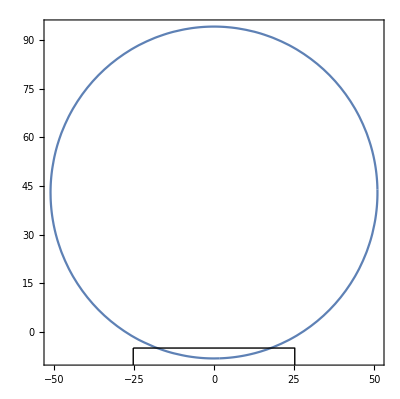

```mathematica
Show[ContourPlot[(x-0)^2+(y-43)^2==51.1^2,{x,-51.1,51.1},{y,-51.1+43,51.1+43},AspectRatio->Automatic],Graphics[{Line[{{ToExpression[axB],-1*ToExpression[ayB]},{ToExpression[axB],-SetPrecision[(dvrowB nrow)/2. -dvrowB/1000.+dy+eps,7]},{ToExpression[axB1],-SetPrecision[(dvrowB nrow)/2. -dvrowB/1000.+dy+eps,7]},{ToExpression[axB1],-1*ToExpression[ayB]},{ToExpression[axB],-1*ToExpression[ayB]}}]}]](*unfinished:all parameters should be set from input file for complete phantom*)
```

```mathematica
NSolve[{(x-0)^2+(y-43)^2==51.1^2,x==ToExpression[axB]},{x,y}]
```

{{x→-25.2501,y→-1.4257},{x→-25.2501,y→87.4257}}

```mathematica
(* Source and Other *)
```

```mathematica
WriteString[ipp,"\nmode p\n"];
```

```mathematica
(*RDUM*)
```

```mathematica
(*RDUM 1 - radius of trajectory of the X-ray tube, cm*)RDUM1=60;
```

```mathematica
(*RDUM 2 - fan angle, degrees*)RDUM2=49.2;
```

```mathematica
(*RDUM 3 - start position of the scan on the z-axis, cm*)RDUM3=Zcentr;
```

```mathematica
(*RDUM 4 scan range, cm;*)(*0 for axial;*)RDUM4=0;
```

```mathematica
(*RDUM 5 - actual beam width, cm*)RDUM5=1;(*1 is first try to do the calculation;3.5 for debug; was 2.6;*)
```

```mathematica
(*RDUM 6 - pitch of the axial acquisition*)(*0 for axial scan*)RDUM6=0;
```

```mathematica
(*RDUM 7 - type of the shaping filter used in the acquisition*)(*2 - small S filter 100 kV
10 - medium M filter 100 kV
12 - flat filter*)RDUM7=10;(*debug*)
```

```mathematica
(*RDUM 8 - Subscript[X, center]*)RDUM8=0;
```

```mathematica
(*RDUM 9 - Subscript[Y, center]*)RDUM9=5.78165;(*manually chosen for head scan*)
```

```mathematica
(*RDUM 10 - Subscript[n, source cell]*)RDUM10=198;
```

```mathematica
(dvsl (nsliMax)-Zcent)
```

-85.8096

```mathematica
If[CT,WriteString[ipp,"RDUM "~~ToString[RDUM1]~~" "~~ToString[RDUM2]~~" "~~ToString[RDUM3]~~" "~~ToString[RDUM4]~~" "~~ToString[RDUM5]~~" "~~ToString[RDUM6]~~" "~~ToString[RDUM7]~~" "~~ToString[RDUM8]~~" "~~ToString[RDUM9]~~" "~~ToString[RDUM10]~~"\n"],www="c SOURCE \n"~~"sdef erg d1 par=2  pos="~~ToString[srcx]~~" "~~ToString[srcy]~~"   "~~ToString[(dvsl (nsliMax)-Zcent)] ~~vec~~" dir d4 \n";
WriteString[ipp,www];EEE=spectrum[[All,1]];int=spectrum[[All,2]];
Nisotopeline=Length[EEE];
si1Card="si1 A ";sp1Card="sp1   ";ccc=" ";

Do[aaa=EEE[[kk]];bbb=ToString[aaa,CharacterEncoding->"ASCII"];si1Card=StringJoin[si1Card,ccc,bbb];nnstring=StringLength[si1Card];If[nnstring>60,If[kk<Nisotopeline,si1Card=StringJoin[si1Card,"&"],Null];
Write[ipp,TextForm[si1Card]];si1Card=" ",Null];
Null,{kk,1,Nisotopeline}];
If[si1Card≠" ",Write[ipp,TextForm[si1Card]],Null];

Do[If[kk==1,aaa=FortranForm[Chop[SetPrecision[int[[kk]],4],5*10^-7]],If[kk>1,aaa=FortranForm[Chop[SetPrecision[int[[kk]],4],5*10^-7]],Null]];
bbb=ToString[aaa,CharacterEncoding->"ASCII"];sp1Card=StringJoin[sp1Card,ccc,bbb];nnstring=StringLength[sp1Card];If[nnstring>60,If[kk<Nisotopeline,sp1Card=StringJoin[sp1Card,"&"],Null];
Write[ipp,TextForm[sp1Card]];sp1Card=" ",Null];
Null,{kk,1,Nisotopeline}];
If[sp1Card≠" ",Write[ipp,TextForm[sp1Card]],Null];dir=N[Cos[ArcTan[√((AppertX[[1]]/2.)^2+(AppertZ[[1]]/2.)^2)/1./RIP[[1]]]]];;
WriteString[ipp,"si4 "~~ToString[dir]~~" 1.\n"]
WriteString[ipp,"sp4 -21 1\n"];www="c tally \n";
WriteString[ipp,www];];
```

```mathematica
(* Creation of Media *)
```

```mathematica
MediafileName=Phantom<>"_media.dat"
```

15M_media.dat

```mathematica
media0 = Import[Phantom<>"_media.dat","Table"];
```

```mathematica
If[Position[Phantom,"A"]≠{},media={media0[[1]],media0[[2]],media0[[3]]},media={Table[StringSplit[media0[[1,i]],_?LetterQ][[1]],{i,3,Length[media0[[1]]]-2}]}]
```

{{1,6,7,8,11,12,15,16,17,19,20,26,53}}

```mathematica
If[Position[Phantom,"A"]≠{},Do[   
 Do[ If[ numMed[[ik]]==media0[[io]][[1]],AppendTo[ media,media0[[io]]],Null]     ,{ik,1,Length[numMed]}]
,{io,4,Length[media0]}],Do[   
 Do[ If[ numMed[[ik]]==media0[[io]][[1]],AppendTo[ media,media0[[io]]],Null]     ,{ik,1,Length[numMed]}]
,{io,2,Length[media0]}]];
```

```mathematica
WriteString[ipp,"c MEDIA\n"];(*tmpLen is Viarenich way: fixed writing first element, ruined writing materials with long descriptions*)
(*Do[tmpLen=Length[media[[im]]];
za="m"~~ToString[media[[im]][[1]]]; word="  $ ";
Do[
 If[media[[im]][[iz]]≠ 0 &&NumberQ[ media[[im]][[iz]]],ww="  "~~ToString[media[[1]][[iz-2-tmpLen+15]] ]~~"000"~~" -"~~ToString[media[[im]][[iz]] ] ;za=za~~ww;
If[StringLength[za] ≥ 67,za=za~~"\n";
WriteString[ipp,za];za="     ",Null],
If[NumberQ[ media[[im]][[iz]]]==  False,word=word~~ToString[media[[im]][[iz]]],Null]]
 ,{iz,2,Length[media[[1]]]+2}];
za=za~~word~~"\n";
WriteString[ipp,za];
Null,{im,4,Length[media]}]*)
```

```mathematica
If[Position[Phantom,"A"]≠{},Do[tmpLen=Length[media[[im]]];za="m"~~ToString[media[[im]][[1]]]; word="  $ ";tmpMedia=Take[media[[im]],-13];Do[If[tmpMedia[[iz]]≠ 0 ,ww="  "~~ToString[media[[1,iz]]]~~"000"~~" -"~~ToString[tmpMedia[[iz]]];za=za~~ww;If[StringLength[za] ≥ 67,za=za~~"\n";WriteString[ipp,za];
za="   ",Null]],{iz,13}];
Do[
If[NumberQ[ media[[im]][[iz]]]&&media[[im]][[iz]]≠ 0 ,Null,
If[NumberQ[ media[[im]][[iz]]]==  False,word=word~~ToString[media[[im]][[iz]]],Null]]
 ,{iz,2,Length[media[[1]]+2]}];za=za~~word~~"\n";
WriteString[ipp,za];
Null,{im,4,Length[media]}],Do[tmpLen=Length[media[[im]]];za="m"~~ToString[media[[im]][[1]]]; word=" $";tmpMedia=Take[media[[im]],{-14,-2}];Do[If[tmpMedia[[iz]]≠ 0 ,ww="  "~~ToString[media[[1,iz]]]~~"000"~~" -"~~ToString[tmpMedia[[iz]]];za=za~~ww;If[StringLength[za] ≥ 67,za=za~~"\n";WriteString[ipp,za];
za="   ",Null]],{iz,13}];If[za=="   ", za="";word="c ", word=" $"];
(*comment*)Do[
If[NumberQ[ media[[im]][[iz]]]&&media[[im]][[iz]]≠ 0 ,Null,
If[NumberQ[ media[[im]][[iz]]]==  False,word=word~~ToString[media[[im]][[iz]]],Null]]
 ,{iz,2,Length[media[[1]]+2]}];za=za~~word~~"\n";
WriteString[ipp,za];
Null,{im,2,Length[media]}];Print["pediatric phantom"]]
```

pediatric phantom

```mathematica
If[CT,WriteString[ipp,"m54 6000 -1 $Carbon (fiber)\n"]];
```

```mathematica
If[TrueQ[CT],Print["CT mode, calculator not enabled"],WriteString[ipp,"m80 82000 -1 $ Lead for curtains\n"]]
```

```mathematica
(* Create end of input file  *)
```

```mathematica
www="c tally ";
WriteString[ipp,www];
If[Length[cell]>1,work="\nfm6 1e12\n*f6:p ";workcells="";Do[  ww=cell[[ic]][[1]]; If[ww==140,,workcells=workcells~~" "~~ToString[ww]];
,{ic,1,Length[cell]}];WriteString[ipp,work];WriteString[ipp,StringTrim[WriteMCNPCard[workcells]]];WriteString[ipp,"\n*f8:p "];WriteString[ipp,StringTrim[WriteMCNPCard[workcells]]];WriteString[ipp,"\nf4:p "];WriteString[ipp,StringTrim[WriteMCNPCard[workcells]]];WriteString[ipp,"\n"];,Null]

www="c parameters  \nnps "~~ToString[200000] ~~"\nlost  20 10 \nprdmp 2j 1 r\nc   void \nc Print 128";
WriteString[ipp,www];
```

```mathematica
Streams[]
```

{OutputStream[…],OutputStream[…],OutputStream[…]}

```mathematica
Close[ipp]
```

15M_1

```mathematica
Directory[]
```

/home/arkady/Documents/17 Jun/fantom110c-9ct/15M

```mathematica
Zcentr=1;
```

```mathematica
Do[Null
,{Zcentr,1,1}](*could be used for rdum processing*)
```

```mathematica
Directory[]
```

/home/arkady/Documents/17 Jun/fantom110c-9ct/15M